```mathematica
<<X`
```

Package-X v2.1.1 [patched 22/08/2020], by Hiren H. Patel
For more information, see the

## 3pt Form-Factor Calculation

### Exact result

We will begin by calculating the form-factor  for the process  through mediation of a lepton flavor-violating scalar. In our notation, the scalar ϕ has interaction . The results can be translated to a lepton flavor-violating ALP with interaction  via the substitution  and . Note that for a pure pseudo-scalar ALP, .

```mathematica
VertexIK =gik*Exp[I*ϕik]*(Cos[θik]𝟙+I*Exp[I*δik]Sin[θik]γ5);
ConjugateVertexJK = gjk*Exp[-I*ϕjk]*(Cos[θjk]𝟙+I*Exp[-I*δjk]Sin[θjk]γ5);;
```

```mathematica
kinematics = {q1.q1->mi^2,q2.q2->mj^2,q1.q2->(mi^2+mj^2)/2,q.q->0};
```

```mathematica
M=-I/(16 π^2)(LoopIntegrate[⟨𝓊[q2,mj],I*VertexIK,I*((q2-q1).γ+k.γ+mk 𝟙),-I*e*Subscript[γ, μ],I*(k.γ+mk 𝟙),I*ConjugateVertexJK,𝓊[q1,mi]⟩,k,{-q1+k,mϕ},{q2-q1+k,mk},{k,mk}])/.kinematics//LoopRefine;
```

```mathematica
FormFactor2IJK=FullSimplify[(32*π^2(mi+mj))/(I*e*ⅇ^(-ⅈ (-ϕik+ϕjk)) gik gjk)*Coefficient[M,⟨𝓊[q2,mj],Subscript[σ, μ,{-q1+q2}],𝓊[q1,mi]⟩]];
```

```mathematica
FormFactor3IJK=FullSimplify[(32*π^2(mi-mj))/(e*ⅇ^(-ⅈ (-ϕik+ϕjk)) gik gjk)*Coefficient[M,⟨𝓊[q2,mj],Subscript[σ, μ,{-q1+q2}],γ5,𝓊[q1,mi]⟩]];
```

The form-factor  is symmetric via swapping of  and j:

```mathematica
FullSimplify[FormFactor2IJK - (FormFactor2IJK/.{mi->mj,mj->mi})]
```

0

And the form factor  is symmetric via swapping and negating  and :

```mathematica
FullSimplify[FormFactor3IJK - (FormFactor3IJK/.{mi->-mj,mj->-mi})]
```

0

The form-factors looks very complicated:

```mathematica
FullSimplify[FormFactor2IJK]
```

1/(2 mi^3 (mi-mj) mj^3 (mi+mj))ⅇ^(-ⅈ δjk) (ⅇ^(ⅈ δjk) Cos[θik] Cos[θjk] (2 mi^3 mj^2 (2 mj mk (mj+mk)-2 mj mϕ^2-mi (mj^2-2 mj mk-mk^2+mϕ^2)) DiscB[mj^2,mk,mϕ]-(mi-mj) (mi+mj) (2 mi^2 mj^2 (mi mj-mk^2+mϕ^2)+(mk^2 (-2 mi^2 mj^2+2 mi mj (mi+mj) mk+(mi+mj)^2 mk^2)-2 (mi+mj) mk (mi mj+(mi+mj) mk) mϕ^2+(mi+mj)^2 mϕ^4) Log[mk^2/mϕ^2]+4 mi^3 mj^3 mk (mi+mj+mk) ScalarC0[0,mi^2,mj^2,mk,mk,mϕ]))+ⅇ^(ⅈ δik) (-2 mi^3 mj^2 (2 mj ((mj-mk) mk+mϕ^2)+mi (mj^2+2 mj mk-mk^2+mϕ^2)) DiscB[mj^2,mk,mϕ]+(mi-mj) (mi+mj) (-2 mi^2 mj^2 (mi mj-mk^2+mϕ^2)+(mk^2 (2 mi^2 mj^2+2 mi mj (mi+mj) mk-(mi+mj)^2 mk^2)+2 (mi+mj) mk (-mi mj+(mi+mj) mk) mϕ^2-(mi+mj)^2 mϕ^4) Log[mk^2/mϕ^2]+4 mi^3 mj^3 (mi+mj-mk) mk ScalarC0[0,mi^2,mj^2,mk,mk,mϕ])) Sin[θik] Sin[θjk]+2 mi^2 mj^3 DiscB[mi^2,mk,mϕ] (ⅇ^(ⅈ δjk) (mi^2 (mj-2 mk)+mj (-mk^2+mϕ^2)+2 mi (-mk (mj+mk)+mϕ^2)) Cos[θik] Cos[θjk]+ⅇ^(ⅈ δik) (mi^2 (mj+2 mk)+2 mi ((mj-mk) mk+mϕ^2)+mj (-mk^2+mϕ^2)) Sin[θik] Sin[θjk]))

It is possible to write them in a simplified form. In particular, we begin by noting that the coefficients of cosine products and sine products are related to each other:

```mathematica
FormFactorCosIKCosJK = FullSimplify[Coefficient[FormFactor2IJK,Cos[θik] Cos[θjk]]];
FormFactorSinIKSinJK =  FullSimplify[Exp[-I*(δik-δjk)]*Coefficient[FormFactor2IJK,Sin[θik] Sin[θjk]]];
FormFactorCosIKSinJK = FullSimplify[Exp[I*δjk]Coefficient[FormFactor3IJK,Cos[θik] Sin[θjk]]];
FormFactorSinIKCosJK =  FullSimplify[Exp[-I*δik]*Coefficient[FormFactor3IJK,Sin[θik] Cos[θjk]]];
```

```mathematica
FullSimplify[FormFactorCosIKCosJK-(FormFactorSinIKSinJK /.{mi->-mi,mj->-mj})]
```

0

```mathematica
FullSimplify[FormFactorCosIKCosJK-(FormFactorCosIKSinJK /.{mi->-mi})]
```

0

```mathematica
FullSimplify[FormFactorCosIKCosJK-(-FormFactorSinIKCosJK /.{mj->-mj})]
```

0

Hence, the form-factors can be written as
						 
 and
						
 We will now work on finding the function . To do so, we will simplify the coefficients of the various functions which appear in the expression derived above, namely DiscB[mi^2,mk,mϕ], DiscB[mj^2,mk,mϕ], Log[mk^2/mϕ^2], ScalarC0[0,mi^2,mj^2,mk,mk,mϕ], and the constant term.

The coefficient of DiscB[mi^2,mk,mϕ]:

```mathematica
FormFactorDiscBIK = FullSimplify[Coefficient[FormFactorCosIKCosJK,DiscB[mi^2,mk,mϕ]]]
```

(mi^2 (mj-2 mk)+mj (-mk^2+mϕ^2)+2 mi (-mk (mj+mk)+mϕ^2))/(mi (mi-mj) (mi+mj))

```mathematica
DiscBIKCoeff[x_,y_,z_]:=FullSimplify[FormFactorDiscBIK/.{mi->x*mϕ,mj->y*mϕ,mk->z*mϕ}];
```

```mathematica
FullSimplify[DiscBIKCoeff[x,y,z]-((2z+y)x^2-(2x+y)(z^2+2x*z-1))/(x(x-y)(x+y))]
```

0

```mathematica
fDiscBIK[x_,y_,z_]:=((2z+y)x^2-(2x+y)(z^2+2x*z-1))/(x(x-y)(x+y));
```

The coefficient of  DiscB[mj^2,mk,mϕ]:

```mathematica
FormFactorDiscBJK = FullSimplify[Coefficient[FormFactorCosIKCosJK,DiscB[mj^2,mk,mϕ]]]
```

(2 mj mk (mj+mk)-2 mj mϕ^2-mi (mj^2-2 mj mk-mk^2+mϕ^2))/((mi-mj) mj (mi+mj))

```mathematica
DiscBJKCoeff[x_,y_,z_]:=FullSimplify[FormFactorDiscBJK/.{mi->x*mϕ,mj->y*mϕ,mk->z*mϕ}];
```

```mathematica
FullSimplify[DiscBJKCoeff[x,y,z]-((2z+x)y^2-(2y+x)(z^2+2y*z-1))/(y(y-x)(y+x))]
```

0

```mathematica
fDiscBJK[x_,y_,z_]:=((2z+x)y^2-(2y+x)(z^2+2y*z-1))/(y(y-x)(y+x));
```

The coefficient of Log[mk^2/mϕ^2]:

```mathematica
FormFactorLog=FullSimplify[Coefficient[FormFactorCosIKCosJK,Log[mk^2/mϕ^2]]]
```

(mk^2 (2 mi^2 mj^2-2 mi mj (mi+mj) mk-(mi+mj)^2 mk^2)+2 (mi+mj) mk (mj mk+mi (mj+mk)) mϕ^2-(mi+mj)^2 mϕ^4)/(2 mi^3 mj^3)

```mathematica
LogCoeff[x_,y_,z_]:=FullSimplify[FormFactorLog/.{mi->x*mϕ,mj->y*mϕ,mk->z*mϕ}];
```

```mathematica
FullSimplify[LogCoeff[x,y,z]-(-(((x+y)(1-z^2)-x*y*z)^2-3(x^2 y^2 z^2))/(2 x^3 y^3))]
```

0

```mathematica
fLog[x_,y_,z_]:=-(((x+y)(1-z^2)-x*y*z)^2-3(x^2 y^2 z^2))/(2 x^3 y^3);
```

The coefficient of ScalarC0[0,mi^2,mj^2,mk,mk,mϕ]:

```mathematica
FormFactorScalarC0=FullSimplify[Coefficient[FormFactorCosIKCosJK,ScalarC0[0,mi^2,mj^2,mk,mk,mϕ]]]
```

-2 mk (mi+mj+mk)

```mathematica
ScalarC0Coeff[x_,y_,z_]:=FullSimplify[1/mϕ^2*FormFactorScalarC0/.{mi->x*mϕ,mj->y*mϕ,mk->z*mϕ}];
```

```mathematica
FullSimplify[ScalarC0Coeff[x,y,z]-(-2(x+y+z)z)]
```

0

```mathematica
fScalarC0[x_,y_,z_]:=-(2(x+y+z)z)/(x+y);
```

And finally, the constant term:

```mathematica
FormFactorConstant = FullSimplify[FormFactorCosIKCosJK-FormFactorLog*Log[mk^2/mϕ^2]-FormFactorScalarC0*ScalarC0[0,mi^2,mj^2,mk,mk,mϕ]-FormFactorDiscBIK*DiscB[mi^2,mk,mϕ]-FormFactorDiscBJK*DiscB[mj^2,mk,mϕ]]
```

-(mi mj-mk^2+mϕ^2)/(mi mj)

```mathematica
ConstantCoeff[x_,y_,z_]:=FullSimplify[FormFactorConstant/.{mi->x*mϕ,mj->y*mϕ,mk->z*mϕ}];
```

```mathematica
ConstantCoeff[x,y,z]
```

(-1-x y+z^2)/(x y)

```mathematica
fConstant[x_,y_,z_]:=-(1+x y-z^2)/(x y);
```

In total, the form factor is given by:

```mathematica
FormFactorCosIKCosJKVerification =(DiscBIKCoeff[mi/mϕ,mj/mϕ,mk/mϕ]* DiscB[mi^2,mk,mϕ]+DiscBJKCoeff[mi/mϕ,mj/mϕ,mk/mϕ]* DiscB[mj^2,mk,mϕ]+ConstantCoeff[mi/mϕ,mj/mϕ,mk/mϕ]+ LogCoeff[mi/mϕ,mj/mϕ,mk/mϕ]*Log[mk^2/mϕ^2]+mϕ^2*ScalarC0Coeff[mi/mϕ,mj/mϕ,mk/mϕ]*ScalarC0[0,mi^2,mj^2,mk,mk,mϕ]);
```

```mathematica
FullSimplify[FormFactorCosIKCosJK-FormFactorCosIKCosJKVerification]
```

0

```mathematica
FormFactor2IJKVerification = FormFactorCosIKCosJKVerification*Cos[θik]Cos[θjk]+
Exp[I*(δik-δjk)](FormFactorCosIKCosJKVerification/.{mi->-mi,mj->-mj})Sin[θik]Sin[θjk];
```

```mathematica
FullSimplify[FormFactor2IJK-FormFactor2IJKVerification]
```

0

```mathematica
FormFactor3IJKVerification =Exp[-I*δjk](FormFactorCosIKCosJKVerification/.{mi->-mi})*Cos[θik]Sin[θjk]-
Exp[I*δik](FormFactorCosIKCosJKVerification/.{mj->-mj})Sin[θik]Cos[θjk];
```

```mathematica
FullSimplify[FormFactor3IJK-FormFactor3IJKVerification]
```

0

At this point, it is worth pointing out that DiscB[mi^2,mk,mϕ]=DiscB[mi^2/mϕ^2,mk/mϕ,1] and ScalarC0[0,mi^2,mj^2,mk,mk,mϕ]=1/mϕ^2 ScalarC0[0,mi^2/mϕ^2,mj^2/mϕ^2,mk/mϕ,mk/mϕ,1]. Hence, the function  is can be rewritten as . This function is mostly tractable, with the exception of the ScalarC0 term, which requires special care. Hence, we will separate this into two terms to make future expansions easier.

```mathematica
fNoC0[x_,y_,z_]:=FullSimplify[(DiscBIKCoeff[x,y,z]* DiscB[x^2,z,1]+(DiscBJKCoeff[x,y,z]* DiscB[y^2,z,1]+ LogCoeff[x,y,z]*Log[z^2]))+ConstantCoeff[x,y,z]];  
fC0[x_,y_,z_]:=ScalarC0Coeff[x,y,z]ScalarC0[0,x^2,y^2,z,z,1];
f[x_,y_,z_]:=fNoC0[x,y,z]+fC0[x,y,z];
```

It turns out to be useful to define (x,y,z)=1/2[f(x,y,z)+f(-x,-y,z)] and =(x,y,z)=1/2[f(x,y,z)-f(-x,-y,z)]. These appear as the form-factors for chirally-coupled interactions, but also factorize the leading and next-to-leading terms.

```mathematica
fPlusNoC0[x_,y_,z_]:=1/2(fNoC0[x,y,z]+fNoC0[-x,-y,z]);
fMinusNoC0[x_,y_,z_]:=1/2(fNoC0[x,y,z]-fNoC0[-x,-y,z]);
fPlusC0[x_,y_,z_]:=1/2(fC0[x,y,z]+fC0[-x,-y,z]);
fMinusC0[x_,y_,z_]:=1/2(fC0[x,y,z]-fC0[-x,-y,z]);
fPlus[x_,y_,z_]:=fPlusNoC0[x,y,z]+fPlusC0[x,y,z];
fMinus[x_,y_,z_]:=fMinusNoC0[x,y,z]+fMinusC0[x,y,z];
```

### Approximations

We now examine   (so ), which is relevant for  with an internal , and  with an internal . For the ScalarC0-free part of  (defining =1/μ_i^2), we have

```mathematica
Assuming[{x>0,y>0},FullSimplify[(Normal[LoopRefineSeries[fPlusNoC0[x,y,x],{y,0,0}]]//DiscExpand//KallenExpand)/.{x->1/Sqrt[xi]}]]
```

-3+2 xi+2 √(-4+xi) (-1+xi) √xi Log[1/2 (√(-4+xi)+√xi)]-(-3+xi) xi Log[xi]

And for the ScalarC0-free part of  is

```mathematica
Assuming[{x>0,y>0},FullSimplify[(Normal[LoopRefineSeries[fMinusNoC0[x,y,x],{y,0,0}]]//DiscExpand//KallenExpand)/.{x->1/Sqrt[xi]}]]
```

2 √(-4+xi) √xi (Log[2]-Log[√(-4+xi)+√xi])-(2 Log[xi])/(-1+xi)+xi Log[xi]-2 (1+Log[xi])

As for the ScalarC0-dependent parts, we see that they are the same:

```mathematica
Assuming[{x>0,y>0},FullSimplify[(Normal[LoopRefineSeries[fPlusC0[x,y,x]//C0Expand//DiscExpand//C0Expand,{y,0,0}]])/.{x->1/Sqrt[xi]}]]
```

2 DiLog[(2 (-2+xi))/(-2+√(-4+xi) √xi+xi),-1+2/xi]+2 DiLog[1/2 (-2+xi) (-2+√(-4+xi) √xi+xi),(-2+xi)/xi]+Log[(2+√(-4+xi) √xi-xi)/(√(-4+xi) √xi+xi)]^2-2 PolyLog[2,(2 (-1+xi))/(-2+√(-4+xi) √xi+xi)]+2 PolyLog[2,(2 (-1+xi))/(√(-4+xi) √xi+xi)]

```mathematica
Assuming[{x>0,y>0},FullSimplify[(Normal[LoopRefineSeries[fMinusC0[x,y,x]//C0Expand//DiscExpand//C0Expand,{y,0,0}]])/.{x->1/Sqrt[xi]}]]
```

2 DiLog[(2 (-2+xi))/(-2+√(-4+xi) √xi+xi),-1+2/xi]+2 DiLog[1/2 (-2+xi) (-2+√(-4+xi) √xi+xi),(-2+xi)/xi]+Log[(2+√(-4+xi) √xi-xi)/(√(-4+xi) √xi+xi)]^2-2 PolyLog[2,(2 (-1+xi))/(-2+√(-4+xi) √xi+xi)]+2 PolyLog[2,(2 (-1+xi))/(√(-4+xi) √xi+xi)]

This appears to have two different forms; one for , and . We can simplify in either case (noting that DiLog[x, y] = DiLog[x, sgn(y)]).  First, assuming .

```mathematica
fC0ApproxLargexi[xi_]:=Assuming[{xi>0},FullSimplify[2 DiLog[(2 (-2+xi))/(-2+√(-4+xi) √xi+xi),-1]+2 DiLog[1/2 (-2+xi) (-2+√(-4+xi) √xi+xi),1]+Log[(2+√(-4+xi) √xi-xi)/(√(-4+xi) √xi+xi)]^2-2 PolyLog[2,(2 (-1+xi))/(-2+√(-4+xi) √xi+xi)]+2 PolyLog[2,(2 (-1+xi))/(√(-4+xi) √xi+xi)]]];
```

```mathematica
FullSimplify[fC0ApproxLargexi[xi]]
```

Log[(2-xi+√((-4+xi) xi))/(xi+√((-4+xi) xi))]^2-Log[-2/(2-2 √((-4+xi) xi)+xi (-4+xi+√((-4+xi) xi)))]^2-2 PolyLog[2,-1/2 (-2+xi) (2-xi+√((-4+xi) xi))]+2 PolyLog[2,(2 (-2+xi))/(-2+xi+√((-4+xi) xi))]-2 PolyLog[2,(2 (-1+xi))/(-2+xi+√((-4+xi) xi))]+2 PolyLog[2,(2 (-1+xi))/(xi+√((-4+xi) xi))]

Then, assuming :

```mathematica
fC0ApproxSmallxi[xi_]:=Assuming[{xi>0},FullSimplify[2 DiLog[(2 (-2+xi))/(-2+√(-4+xi) √xi+xi),1]+2 DiLog[1/2 (-2+xi) (-2+√(-4+xi) √xi+xi),-1]+Log[(2+√(-4+xi) √xi-xi)/(√(-4+xi) √xi+xi)]^2-2 PolyLog[2,(2 (-1+xi))/(-2+√(-4+xi) √xi+xi)]+2 PolyLog[2,(2 (-1+xi))/(√(-4+xi) √xi+xi)]]]
```

```mathematica
FullSimplify[fC0ApproxSmallxi[xi]]
```

-Log[(-2+xi+√((-4+xi) xi))/(2-xi+√((-4+xi) xi))]^2+Log[(2-xi+√((-4+xi) xi))/(xi+√((-4+xi) xi))]^2-2 PolyLog[2,(2 (-1+xi))/(-2+xi+√((-4+xi) xi))]+2 PolyLog[2,(2 (-1+xi))/(xi+√((-4+xi) xi))]

We can plot them to see how they compare in the respective regions, Their real parts always seem to match:

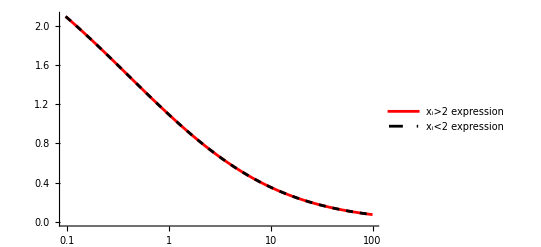

```mathematica
LogLinearPlot[{Re[fC0ApproxLargexi[xi]],Re[fC0ApproxSmallxi[xi]]},{xi,0,100},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"x_i>2 expression","x_i<2 expression"}]
```

But their imaginary parts differ after :

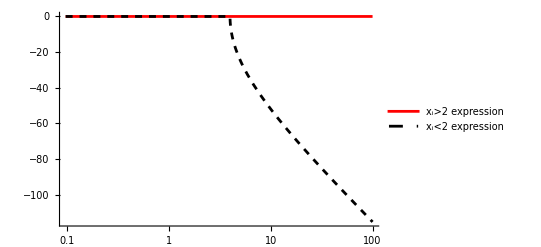

```mathematica
LogLinearPlot[{Im[fC0ApproxLargexi[xi]],Im[fC0ApproxSmallxi[xi]]},{xi,0,100},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"x_i>2 expression","x_i<2 expression"}]
```

It appears that the expression for >2 also matches the expression for  (which only differs in the imaginary part for ), so we can use that term to represent the the form-factor in both cases. We can use some PolyLog identities to get this term into the form
						 
						 
and we can plot them to ensure they are the same:

```mathematica
fC0Approx[xi_]:=-Log[(xi+Sqrt[xi*(xi-4)])/(2xi)]^2-2PolyLog[2,1-xi]-2PolyLog[2,(xi-Sqrt[xi(xi-4)])/(2xi)]+2PolyLog[2,(2-xi-Sqrt[xi*(xi-4)])/2];
```

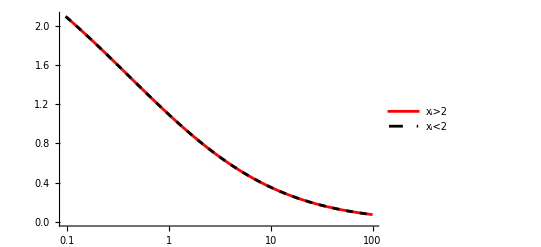

```mathematica
LogLinearPlot[{Re[fC0ApproxLargexi[xi]],Re[fC0Approx[xi]]},{xi,0,100},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"x_i>2","x_i<2"}]
```

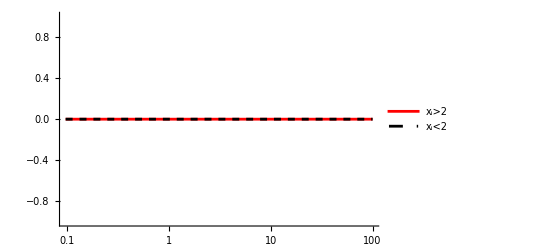

```mathematica
LogLinearPlot[{Im[fC0ApproxLargexi[xi]],Im[fC0Approx[xi]]},{xi,0,100},PlotRange->{-1,1},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"x_i>2","x_i<2"}]
```

So  and  are given by

						

and

#### ,k

We now examine   (so ), which is relevant for  and  with an internal  or . For the ScalarC0-free part of  We have

```mathematica
Assuming[{x>0,x<1,y>0,z>0, t>0,xi>0},FullSimplify[(Normal[LoopRefineSeries[fPlusNoC0[x,t*y,t*z]//DiscExpand//KallenExpand,{t,0,0}]]/.{t->1})/.{x->1/Sqrt[xi]}]]
```

-1+2 xi+2 (-1+xi) xi Log[(-1+xi)/xi]

```mathematica
Assuming[{x>0,x<1,y>0,z>0, t>0,xi>0},FullSimplify[(Normal[LoopRefineSeries[fMinusNoC0[x,t*y,t*z]//DiscExpand//KallenExpand,{t,0,2}]]/.{t->1})/.{x->1/Sqrt[xi],y->μj,z->μk}]]
```

-2 √xi (1+√xi μj) μk (1+(-1+xi) Log[(-1+xi)/xi])

Although we have chosen  in the assumptions, it turns out this is valid for all  as long as we choose the branch . Moving onto the C0-dependent pieces, we have for :

```mathematica
Assuming[{x>0,x<1,y>0,z>0, t>0,xi>0},FullSimplify[Normal[LoopRefineSeries[fPlusC0[x,t*y,t*z]//C0Expand//DiscExpand//KallenExpand,{t,0,1}]]/.{t->1}]]
```

0

This is at a higher order in , so can be ignored. Looking instead at the ScalarC0 part of , we have

```mathematica
Assuming[{x>0,x<1,y>0,z>0, t>0,xi>0},FullSimplify[Normal[LoopRefineSeries[fMinusC0[x,t*y,t*z]//C0Expand//DiscExpand//KallenExpand,{t,0,1}]]/.{t->1}]]
```

1/(3 x)z (π^2-6 DiLog[(2 (-1+z^2))/(-1+x^2+z^2+√((-1+x^2)^2-2 (1+x^2) z^2+z^4)),1-z^2]+6 DiLog[(2 (-1+x^2+z^2))/(-1+x^2+z^2+√(x^4+(-1+z^2)^2-2 x^2 (1+z^2))),1-x^2-z^2]+6 DiLog[(2 (-1+z^2))/(-1+y^2+z^2+√(y^4+(-1+z^2)^2-2 y^2 (1+z^2))),1-z^2]-6 DiLog[(2 (-1+y^2+z^2))/(-1+y^2+z^2+√(y^4+(-1+z^2)^2-2 y^2 (1+z^2))),1-y^2-z^2]-6 PolyLog[2,1/(1-x^2)])

We will operate under the assumption that  and  are small. Then, 1-z^2>0, -1+z^2<0, and 1-y^2-z^2>0. In addition, let us assume 1-x^2-z^2>0 and -1+x^2+z^2<0. Then,

```mathematica
Assuming[{x>0,x<1,y>0,z>0, t>0,xi>0,xk>0},FullSimplify[(Normal[Series[1/(3 x)z (π^2-6 DiLog[(2 (-1+z^2))/(-1+x^2+z^2+√((-1+x^2)^2-2 (1+x^2) z^2+z^4)),1]+6 DiLog[(2 (-1+x^2+z^2))/(-1+x^2+z^2+√(x^4+(-1+z^2)^2-2 x^2 (1+z^2))),1]+6 DiLog[(2 (-1+z^2))/(-1+y^2+z^2+√(y^4+(-1+z^2)^2-2 y^2 (1+z^2))),1]-6 DiLog[(2 (-1+y^2+z^2))/(-1+y^2+z^2+√(y^4+(-1+z^2)^2-2 y^2 (1+z^2))),1]-6 PolyLog[2,1/(1-x^2)])/.{y->t*y,z->t*z},{t,0,2}]]/.{t->1})/.{x->1/Sqrt[xi],z->1/Sqrt[xk]}]]
```

1/3 √(xi/xk) ((π+3 ⅈ Log[(-1+xi)/xi])^2-6 Log[(-1+xi)/xi] Log[xi xk]-6 PolyLog[2,xi/(-1+xi)])

Using Polylog identities, this can be rewritten to be of the form

.

```mathematica
fC0Approx1[xi_,xk_]:=1/3((π+3 ⅈ Log[(-1+xi)/xi])^2-6 Log[(-1+xi)/xi] Log[xi *xk]-6 PolyLog[2,xi/(-1+xi)]);
fC0Approx2[xi_,xk_]:=-2(Log[((xi-1)xk)/xi]Log[(xi-1)/xi]+PolyLog[2,1/xi]);
```

We can verify this by plotting for various xk:

```mathematica
Manipulate[LogLinearPlot[{Re[fC0Approx1[xi,10^exp]],Re[fC0Approx2[xi,10^exp]]},{xi,0,10},PlotStyle->{Black,{Red,Dashed}}],{exp,-2,2}]
```

```mathematica
Manipulate[LogLinearPlot[{Im[fC0Approx2[xi,10^exp]],Im[fC0Approx1[xi,10^exp]]},{xi,0,10},PlotStyle->{Black,{Red,Dashed}}],{exp,-2,2}]
```

So combining this with the ScalarC0-independent piece, we have for :
 
		.

We note here that despite being suppressed by , the second term is not always that small relative to the first. This is explored in more detail in the attached Python notebook. In particular, it is roughly the same size or larger for τ→μγ through a μ:

CompiledFunction::cfn: Numerical error encountered at instruction 19344; proceeding with uncompiled evaluation.

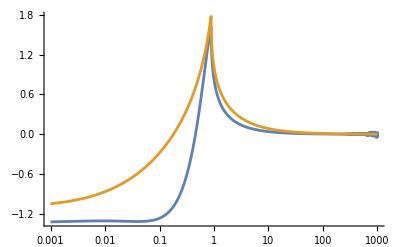

```mathematica
LogLinearPlot[{Re[fPlus[1.77/(Sqrt[x]1.77),0.106/(Sqrt[x]1.77),0.106/(Sqrt[x]1.77)]],Re[fMinus[1.77/(Sqrt[x]1.77),0.106/(Sqrt[x]1.77),0.106/(Sqrt[x]1.77)]]},{x,10^-3,10^3}]
```

#### :

Finally, we examine the scenario , which is relevant for  with an internal . In this scenario, it turns out that the ScalarC0 term is well-behaved enough that we don’t need to treat it separately. We have:

```mathematica
Assuming[{x>0,x<1,y>0,z>0,xk>0,xk!=1},FullSimplify[Normal[LoopRefineSeries[fPlus[t*x,t*y,z],{t,0,2}]]]]
```

(t^2 (x+y)^2 (2+3 z^2-6 z^4+z^6+12 z^2 Log[z]))/(6 (-1+z^2)^4)

```mathematica
Assuming[{x>0,x<1,y>0,z>0,xk>0,xk!=1},FullSimplify[(Normal[LoopRefineSeries[fPlus[t*x,t*y,z],{t,0,2}]]/.{t->1})/.{z->1/Sqrt[xk]}]]
```

(xk (x+y)^2 ((-1+xk) (-1+xk (5+2 xk))-6 xk^2 Log[xk]))/(6 (-1+xk)^4)

```mathematica
Assuming[{x>0,y>0,z>0, xk>0},Normal[FullSimplify[(LoopRefineSeries[fMinus[t*x,t*y,z],{t,0,1}])/.{z->1/Sqrt[xk]}]]/.{t->1}]
```

(√xk (x+y) (-1+(4-3 xk) xk+2 xk^2 Log[xk]))/(-1+xk)^3

So the form-factors are given by
							,							
							.

## Dipole moments

For the dipole moments, we perform the same sequence of steps, but with  (and relabeling ):

```mathematica
VertexIJ =gij*Exp[I*ϕij]*(Cos[θij]𝟙+I*Exp[I*δij]Sin[θij]γ5);
ConjugateVertexIJ = gij*Exp[-I*ϕij]*(Cos[θij]𝟙+I*Exp[-I*δij]Sin[θij]γ5);;
```

```mathematica
kinematics = {q1.q1->mi^2,q2.q2->mi^2,q1.q2->mi^2,q.q->0};
```

```mathematica
M=-I/(16 π^2)(LoopIntegrate[⟨𝓊[q2,mi],I*VertexIJ,I*((q2-q1).γ+k.γ+mj 𝟙),-I*e*Subscript[γ, μ],I*(k.γ+mj 𝟙),I*ConjugateVertexIJ,𝓊[q1,mi]⟩,k,{-q1+k,mϕ},{q2-q1+k,mj},{k,mj}])/.kinematics//LoopRefine;
```

The magnetic and electric dipole form-factors are then:

```mathematica
FormFactor2IJ=FullSimplify[(32*π^2 2mi)/(I*e*  gij^2)Coefficient[M,⟨𝓊[q2,mi],Subscript[σ, μ,{-q1+q2}],𝓊[q1,mi]⟩]];
```

```mathematica
FormFactor3IJ=FullSimplify[(32*π^2 2mi)/(e*gij^2)Coefficient[M,⟨𝓊[q2,mi],Subscript[σ, μ,{-q1+q2}],γ5,𝓊[q1,mi]⟩]];
```

```mathematica
Collect[FormFactor2IJ,Cos[2θij],FullSimplify]
```

(4 (mi^4 mj^2+(mj^2-mϕ^2)^3+mi^2 (-2 mj^4+mj^2 mϕ^2+mϕ^4)) DiscB[mi^2,mj,mϕ])/(mi^2 Kallenλ[mi^2,mj^2,mϕ^2])+(2 mj Cos[2 θij] (2 mi^2+(2 mi^2 ((mi^2-mj^2)^2-2 mj^2 mϕ^2+mϕ^4) DiscB[mi^2,mj,mϕ])/Kallenλ[mi^2,mj^2,mϕ^2]+(mi^2-mj^2+mϕ^2) Log[mj^2/mϕ^2]))/mi^3-(2 (mi^2 (mi^2-2 mj^2+2 mϕ^2)+(-mi^2 mj^2+(mj^2-mϕ^2)^2) Log[mj^2/mϕ^2]))/mi^4

```mathematica
FullSimplify[FormFactor3IJ]
```

-1/(mi^3 Kallenλ[mi^2,mj^2,mϕ^2])ⅇ^(-ⅈ δij) (1+ⅇ^(2 ⅈ δij)) mj (2 mi^2 ((mi^2-mj^2)^2-2 mj^2 mϕ^2+mϕ^4) DiscB[mi^2,mj,mϕ]+Kallenλ[mi^2,mj^2,mϕ^2] (2 mi^2+(mi^2-mj^2+mϕ^2) Log[mj^2/mϕ^2])) Sin[2 θij]

At first glance, the form factor  appears to have the same functional form as the coefficient of  in . We can test this by parametrizing  as

							
then,  should be 

							.

Let us begin by calculating . We have

```mathematica
gMinus[x_,y_]:=Assuming[{mϕ>0,x>0,y>0},FullSimplify[(Coefficient[FormFactor2IJ,Cos[2θij]]/.{mi->x*mϕ,mj->y*mϕ})//KallenExpand]];
```

```mathematica
FullSimplify[gMinus[x,y]]
```

(4 y (x^2+(x^2 (1+x^4-2 (1+x^2) y^2+y^4) DiscB[mϕ^2 x^2,mϕ,mϕ y])/((-1+x^2)^2-2 (1+x^2) y^2+y^4)+(1+x^2-y^2) Log[y]))/x^3

The dependence on mϕ is superficial, because  DiscB[mϕ^2 x^2,mϕ,mϕ y]= DiscB[x^2,1,y]= DiscB[x^2,y,1]. It is apparent that we can write  in the form

					.
We can explicitly check that this is the same as above:

```mathematica
Assuming[{mϕ>0},FullSimplify[(gMinus[x,y]-(4y)/x(1+(1+x^2-y^2)/x^2 Log[y]+((1+x^2-y^2)^2-2 x^2)/((1+x^2-y^2)^2-4 x^2)DiscB[x^2,y,1]))//DiscExpand//KallenExpand]]
```

0

Moving on to , we have:

```mathematica
gPlus[x_,y_]:=Assuming[{mϕ>0,x>0,y>0},FullSimplify[(FormFactor2IJ-Cos[2θij]gMinus[x,y])/.{mi->x*mϕ,mj->y*mϕ}//KallenExpand]];
```

```mathematica
gPlus[x,y]
```

(4 (x^4 y^2+(-1+y^2)^3+x^2 (1+y^2-2 y^4)) DiscB[mϕ^2 x^2,mϕ,mϕ y])/(x^2 (x^4+(-1+y^2)^2-2 x^2 (1+y^2)))-(2 (x^2 (2+x^2-2 y^2)+2 (1-(2+x^2) y^2+y^4) Log[y]))/x^4

So we can write   in the form

				.
		
Verifying this is the same, we have:

```mathematica
Assuming[{mϕ>0},FullSimplify[(gPlus[x,y]-(-2/x^2(2+x^2-2 y^2+(2(1-y^2)^2-2 x^2 y^2)/x^2 Log[y]-(2(x^4-(1-y^2)((1+x^2-y^2)^2-3 x^2)))/((1+x^2-y^2)^2-4 x^2)DiscB[x^2,y,1])))//DiscExpand//KallenExpand]]
```

0

We can double-check that  is also the relevant function for the form factor :

```mathematica
gMinus2[x_,y_]:=Assuming[{mϕ>0,x>0,y>0},FullSimplify[1/(Sin[2θij]Cos[δij])(-FormFactor3IJ/.{mi->x*mϕ,mj->y*mϕ})//KallenExpand]]
```

```mathematica
FullSimplify[gMinus2[x,y]-gMinus[x,y]]
```

0

Before we look at some useful approximations of these form-factors, let us verify that we can recover these diagonal form-factors from the off-diagonal form-factors with . In particular, from matching  to , we expect

									
and

									.

```mathematica
gPlusLimit[x_,y_]:=Assuming[{x>0,y>0},FullSimplify[LoopRefine[Limit[fPlus[x,z,y],{z->x}]]]];
```

```mathematica
Assuming[{mϕ>0,x>0,y>0},FullSimplify[(gPlusLimit[x,y]-gPlus[x,y])//DiscExpand//KallenExpand]]
```

0

```mathematica
gMinusLimit[x_,y_]:=Assuming[{x>0,y>0},FullSimplify[LoopRefine[Limit[fMinus[x,z,y],{z->x}]]]];
```

```mathematica
Assuming[{mϕ>0,x>0,y>0},FullSimplify[(gMinusLimit[x,y]-gMinus[x,y])//DiscExpand//KallenExpand]]
```

0

As anticipated. Matching  to  on the other hand, we expect

								

and

For some reason, Mathematica thinks the  limit of  is indeterminant. However, if we take a series expansion of  around , we have:

```mathematica
Assuming[{y>0,x>0},FullSimplify[LoopRefineSeries[(x+z)/(x-z)fPlus[x,-z,y],{z,x,0}]]]
```

O[z-x]^1

So the limit is clearly zero. On the other hand, the limit for  gives

```mathematica
Assuming[{y>0,x>0},FullSimplify[LoopRefineSeries[(x+z)/(x-z)fMinus[x,-z,y],{z,x,0}]]]
```

(4 y (x^2+(x^2 (1+x^4-2 (1+x^2) y^2+y^4) DiscB[x^2,1,y])/Kallenλ[1,x^2,y^2]+(1+x^2-y^2) Log[y]))/x^3+O[z-x]^1

Which is just , as expected.

### Approximations

Now we can define and expand (x, y) and  under various limits. There are three cases to consider: , , and .

```mathematica
Assuming[{xi>0,xj>0},FullSimplify[Normal[Series[gPlus[x,y],{y,0,0}]]/.{x->1/Sqrt[xi],y->1/Sqrt[xj]}]]
```

-2-4 xi+4 xi^2 Log[xi/(-1+xi)]

```mathematica
Assuming[{xi>0,xj>0},FullSimplify[Normal[Series[gMinus[x,y],{y,0,2}]]/.{x->1/Sqrt[xi],y->1/Sqrt[xj]}]]
```

-(4 √(xi/xj) (1-xi+xi^2 Log[xi/(-1+xi)]+Log[xi/((-1+xi) xj)]))/(-1+xi)

```mathematica
Assuming[{xi>0,xj>0,mϕ>0},FullSimplify[(gPlus[x,x]//DiscExpand//KallenExpand)/.{x->1/Sqrt[xi]}]]
```

2-4 xi-(4 xi (2+(-4+xi) xi) Log[1/2 (√(-4+xi)+√xi)])/(√((-4+xi) xi))+2 (-2+xi) xi Log[xi]

```mathematica
Assuming[{xi>0,xj>0,mϕ>0},FullSimplify[(gMinus[x,x]//DiscExpand//KallenExpand)/.{x->1/Sqrt[xi]}]]
```

4+(4 (-2+xi) xi Log[1/2 (√(-4+xi)+√xi)])/(√((-4+xi) xi))-2 xi Log[xi]

```mathematica
Assuming[{xi>0,xj>0},FullSimplify[Normal[Series[gPlus[x,y],{x,0,2}]]/.{x->1/Sqrt[xi],y->1/Sqrt[xj]}]]
```

(2 xj ((-1+xj) (-1+xj (5+2 xj))-6 xj^2 Log[xj]))/(3 xi (-1+xj)^4)

```mathematica
Assuming[{xi>0,xj>0},FullSimplify[Normal[Series[gMinus[x,y],{x,0,1}]]/.{x->1/Sqrt[xi],y->1/Sqrt[xj]}]]
```

(2 xj (-1+(4-3 xj) xj+2 xj^2 Log[xj]))/((-1+xj)^3 √(xi xj))

```mathematica
Assuming[{x>0},FullSimplify[Normal[Series[gPlus[x, x],{x,0,4}]]/.{x->1/Sqrt[xi]}]]
```

(25+4 xi-12 Log[xi])/(3 xi^2)

```mathematica
Assuming[{x>0},FullSimplify[Normal[Series[gMinus[x, x],{x,0,4}]]/.{x->1/Sqrt[xi]}]]
```

-(2 (32+9 xi-6 (4+xi) Log[xi]))/(3 xi^2)

```mathematica
fP[x_]:=2x-3-(x-3)x*Log[x]+2*(x-1)*Sqrt[x(x-4)]Log[(x+Sqrt[x*(x-4)])/(2Sqrt[x])]-Log[(x+Sqrt[x*(x-4)])/(2x)]^2-2PolyLog[2,1-x]-2PolyLog[2,(x-Sqrt[x(x-4)])/(2x)]+2PolyLog[2,(2-x-Sqrt[x(x-4)])/2];
fM[x_]:=-2+(x-3)/(x-1)x*Log[x]-2*Sqrt[x(x-4)]Log[(x+Sqrt[x*(x-4)])/(2Sqrt[x])]-Log[(x+Sqrt[x*(x-4)])/(2x)]^2-2PolyLog[2,1-x]-2PolyLog[2,(x-Sqrt[x(x-4)])/(2x)]+2PolyLog[2,(2-x-Sqrt[x(x-4)])/2];
```

```mathematica
Series[fP[x],{x,∞,1}]
```

1/(3 x)+O[1/x]^(3/2)

```mathematica
Series[fM[x],{x,∞,1}]
```

(-3+2 Log[x])/x+O[1/x]^(3/2)

```mathematica
N[fP[100]]
```

0.0030554

```mathematica
N[fM[100]]
```

0.064619

```mathematica
Series[fP[x]+fM[x],{x,∞,1}]
```

(2 (-4+3 Log[x]))/(3 x)+O[1/x]^(3/2)

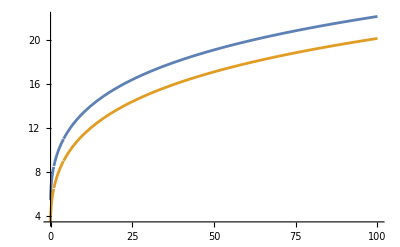

```mathematica
Plot[{(fM[x]+fP[x])/fP[x],(fM[x]-fP[x])/fP[x]},{x,0,100}]
```